```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/deltaT_40/data

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../LQCDdata/hotdpt4u.dat"]];
Tcl=156;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];

WBp2025=Flatten[Import["../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

```mathematica
chi0=Flatten[Import["./chi0.dat"]];
chi1=Flatten[Import["./chi1.dat"]];
chi2=Flatten[Import["./chi2.dat"]];
chi3=Flatten[Import["./chi3.dat"]];
chi4=Flatten[Import["./chi4.dat"]];
chi5=Flatten[Import["./chi5.dat"]];
chi6=Flatten[Import["./chi6.dat"]];
chi7=Flatten[Import["./chi7.dat"]];
chi8=Flatten[Import["./chi8.dat"]];
T=Flatten[Table[21+(i-1),{i,1,280}]];
c0=Transpose[{T/184,chi0/T^4}];
c1=Transpose[{T,-4*chi0/T^5+chi1/T^4}];
c2=Transpose[{T,20*chi0/T^6-8*chi1/T^5+chi2/T^4}];
c3=Transpose[{T,-(120 chi0)/T^7+(60 chi1)/T^6-(12 chi2)/T^5+chi3/T^4}];
c4=Transpose[{T,(840 chi0)/T^8-(480 chi1)/T^7+(120 chi2)/T^6-(16 chi3)/T^5+chi4/T^4}];
cs2=Transpose[{T/184,chi1/(T*chi2)}];
```

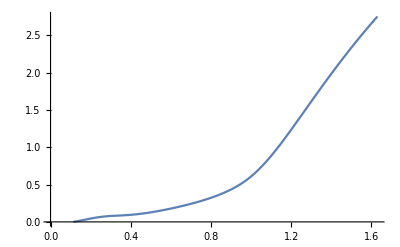

```mathematica
ListLinePlot[c0]
```

### Plot

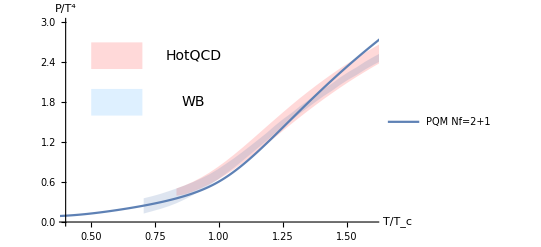

```mathematica
PlotP=Show[ListLinePlot[{c0,Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,3}}],Graphics[{Text[Style["HotQCD",14],{0.9,2.5}],LightRed,Rectangle[{0.5,2.3},{0.7,2.7}]}],Graphics[{Text[Style["WB",14],{0.9,1.8}],LightBlue,Rectangle[{0.5,1.6},{0.7,2.}]}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}}(*,FillingStyle->LightBlue*),PlotStyle->{None,None}],AxesLabel->{"T/T_c","P/T^4"}]
```

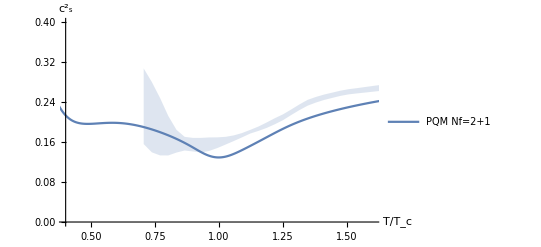

```mathematica
Plotcs2=Show[ListLinePlot[{cs2},FillingStyle->LightRed,PlotStyle->{Automatic,Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,0.4}}],ListLinePlot[{WBcsdown,WBcsup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","(c^2)_s"}]
```

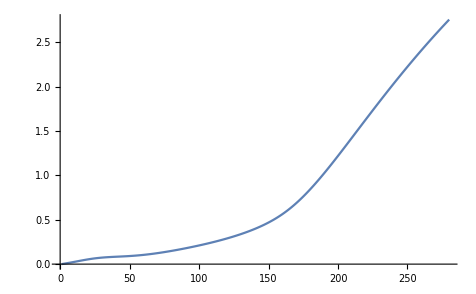

```mathematica
plotc0=ListLinePlot[chi0/T^4]
```

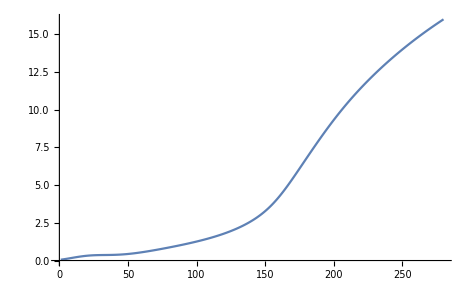

```mathematica
plotc1=ListLinePlot[chi1/T^3]
```

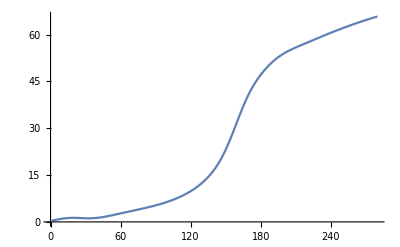

```mathematica
plotc2=ListLinePlot[chi2/T^2]
```

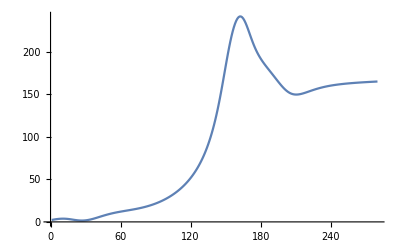

```mathematica
plotc3=ListLinePlot[chi3/T]
```

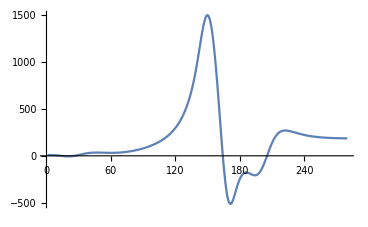

```mathematica
plotc4=ListLinePlot[chi4,PlotRange->All]
```

```mathematica
Export["./PoT4.pdf",PlotP];
Export["./cs2.pdf",Plotcs2];
Export["./c1.pdf",plotc1];
Export["./c2.pdf",plotc2];
Export["./c3.pdf",plotc3];
Export["./c4.pdf",plotc4];
```